```mathematica
<<PlotLegends`
```

```mathematica
myrtaceae120161130=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\myrtaceae\\1_20161130.xlsx"];
myrtaceae220161130=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\myrtaceae\\2_20161130.xlsx"];
myrtaceae320161130=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\myrtaceae\\3_20161130.xlsx"];
myrtaceae420161130=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\myrtaceae\\4_20161130.xlsx"];
```

```mathematica
tempo=Table[myrtaceae120161130[[1,i,1]],{i,1,Length[myrtaceae120161130[[1]]]}];
```

```mathematica
transp120161130=Table[myrtaceae120161130[[1,i,2]],{i,1,Length[tempo]}];
transp220161130=Table[myrtaceae220161130[[1,i,2]],{i,1,Length[tempo]}];
transp320161130=Table[myrtaceae320161130[[1,i,2]],{i,1,Length[tempo]}];
transp420161130=Table[myrtaceae420161130[[1,i,2]],{i,1,Length[tempo]}];
```

```mathematica
par120161130=Table[myrtaceae120161130[[1,i,3]],{i,1,Length[tempo]}];
par220161130=Table[myrtaceae220161130[[1,i,3]],{i,1,Length[tempo]}];
par320161130=Table[myrtaceae320161130[[1,i,3]],{i,1,Length[tempo]}];
par420161130=Table[myrtaceae420161130[[1,i,3]],{i,1,Length[tempo]}];
```

```mathematica
dpv120161130=Table[myrtaceae120161130[[1,i,4]],{i,1,Length[tempo]}];
dpv220161130=Table[myrtaceae220161130[[1,i,4]],{i,1,Length[tempo]}];
dpv320161130=Table[myrtaceae320161130[[1,i,4]],{i,1,Length[tempo]}];
dpv420161130=Table[myrtaceae420161130[[1,i,4]],{i,1,Length[tempo]}];
```

```mathematica
transpVsTempo120161130=N[Table[{tempo[[i]],transp120161130[[i]]},{i,1,Length[tempo]}]];
transpVsTempo220161130=N[Table[{tempo[[i]],transp220161130[[i]]},{i,1,Length[tempo]}]];
transpVsTempo320161130=N[Table[{tempo[[i]],transp320161130[[i]]},{i,1,Length[tempo]}]];
transpVsTempo420161130=N[Table[{tempo[[i]],transp420161130[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
parVsTempo120161130=N[Table[{tempo[[i]],par120161130[[i]]},{i,1,Length[tempo]}]];
parVsTempo220161130=N[Table[{tempo[[i]],par220161130[[i]]},{i,1,Length[tempo]}]];
parVsTempo320161130=N[Table[{tempo[[i]],par320161130[[i]]},{i,1,Length[tempo]}]];
parVsTempo420161130=N[Table[{tempo[[i]],par420161130[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
dpvVsTempo120161130=N[Table[{tempo[[i]],dpv120161130[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo220161130=N[Table[{tempo[[i]],dpv220161130[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo320161130=N[Table[{tempo[[i]],dpv320161130[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo420161130=N[Table[{tempo[[i]],dpv420161130[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobrePAR120161130=Table[transp120161130[[i]]/par120161130[[i]],{i,2,Length[tempo]}];
transpSobrePAR220161130=Table[transp220161130[[i]]/par220161130[[i]],{i,2,Length[tempo]}];
transpSobrePAR320161130=Table[transp320161130[[i]]/par320161130[[i]],{i,2,Length[tempo]}];transpSobrePAR420161130=Table[transp420161130[[i]]/par420161130[[i]],{i,2,Length[tempo]}];
```

```mathematica
transpSobrePARVsTempo120161130=N[Table[{tempo[[i]],transpSobrePAR120161130[[i]]},{i,1,Length[tempo]}]];
transpSobrePARVsTempo220161130=N[Table[{tempo[[i]],transpSobrePAR220161130[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo320161130=N[Table[{tempo[[i]],transpSobrePAR320161130[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo420161130=N[Table[{tempo[[i]],transpSobrePAR420161130[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobreDPV120161130=Table[transp120161130[[i]]/dpv120161130[[i]],{i,1,Length[tempo]}];
transpSobreDPV220161130=Table[transp220161130[[i]]/dpv220161130[[i]],{i,1,Length[tempo]}];
transpSobreDPV320161130=Table[transp320161130[[i]]/dpv320161130[[i]],{i,1,Length[tempo]}];transpSobreDPV420161130=Table[transp420161130[[i]]/dpv420161130[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobreDPVVsTempo120161130=N[Table[{tempo[[i]],transpSobreDPV120161130[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo220161130=N[Table[{tempo[[i]],transpSobreDPV220161130[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo320161130=N[Table[{tempo[[i]],transpSobreDPV320161130[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo420161130=N[Table[{tempo[[i]],transpSobreDPV420161130[[i]]},{i,1,Length[tempo]}]];
```

## Myrtaceae - 30/11/2016 - Transpiração

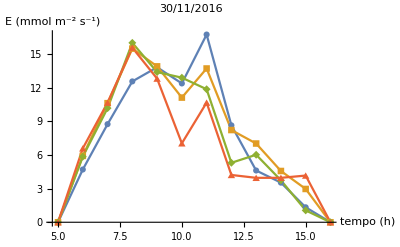

```mathematica
g1=ListLinePlot[{transpVsTempo120161130,transpVsTempo220161130,transpVsTempo320161130,transpVsTempo420161130},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.12MPa"},LegendPosition->{.7,-0.4},PlotLabel->"30/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E (mmol m^-2 s^-1)"}]
```

## Myrtaceae - 30/11/2016 - PAR ( radiação fotossinteticamente ativa)

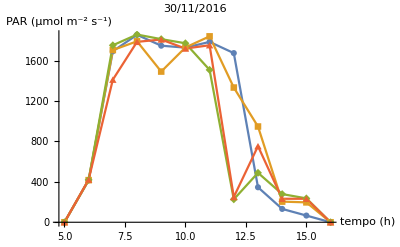

```mathematica
g2=ListLinePlot[{parVsTempo120161130,parVsTempo220161130,parVsTempo320161130,parVsTempo420161130},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.12MPa"},LegendPosition->{.7,-0.4},PlotLabel->"30/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","PAR (μmol m^-2 s^-1)"}]
```

## Myrtaceae - 30/11/2016 - DPV (déficit de pressão de vapor)

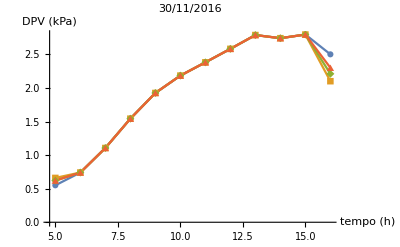

```mathematica
g3=ListLinePlot[{dpvVsTempo120161130,dpvVsTempo220161130,dpvVsTempo320161130,dpvVsTempo420161130},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.12MPa"},LegendPosition->{.7,-0.4},PlotLabel->"30/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","DPV (kPa)"}]
```

## Myrtaceae - 30/11/2016 - Relação Transpiração - PAR

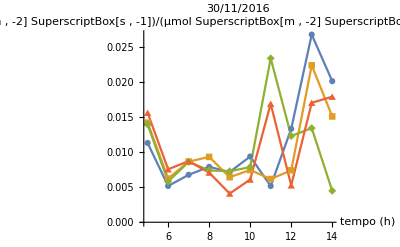

```mathematica
g4=ListLinePlot[{transpSobrePARVsTempo120161130,transpSobrePARVsTempo220161130,transpSobrePARVsTempo320161130,transpSobrePARVsTempo420161130},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.12MPa"},LegendPosition->{.7,-0.4},PlotLabel->"30/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/PAR ((mol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/(μmol SuperscriptBox[m , -2] SuperscriptBox[s , -1]))"}]
```

## Myrtaceae - 30/11/2016 - Relação Transpiração - DPV

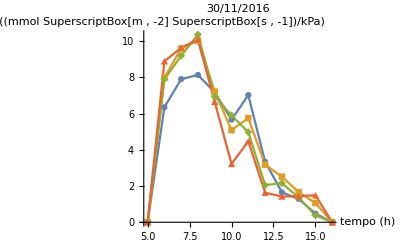

```mathematica
g5=ListLinePlot[{transpSobreDPVVsTempo120161130,transpSobreDPVVsTempo220161130,transpSobreDPVVsTempo320161130,transpSobreDPVVsTempo420161130},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.12MPa"},LegendPosition->{.7,-0.4},PlotLabel->"30/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/DPV ((mmol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/kPa)"}]
```